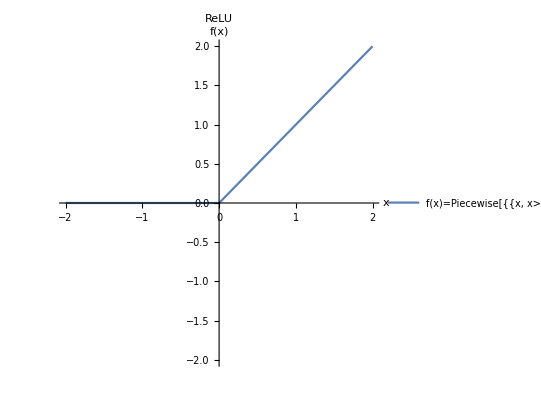

```mathematica
relu=Plot[Ramp[x], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=Piecewise[{{x, x>0}, {0, x≤0}}]"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["ReLU",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\ReLU.jpg",relu]
```

C:\Modulation\Activation functions\ReLU.jpg

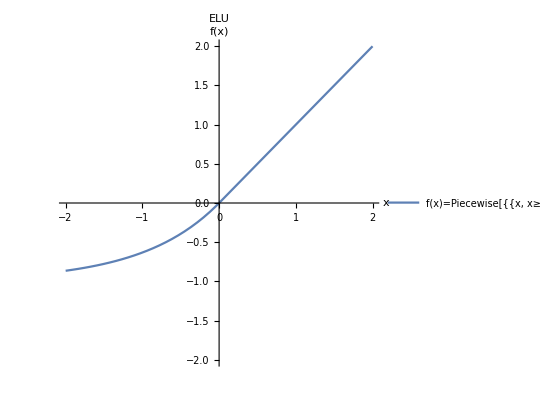

```mathematica
elu=Plot[Piecewise[{{Exp[x]-1,x<0},{x,x>0}}], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=Piecewise[{{x, x≥0}, {e^x-1, x<0}}]"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["ELU",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\ELU.jpg",elu]
```

C:\Modulation\Activation functions\ELU.jpg

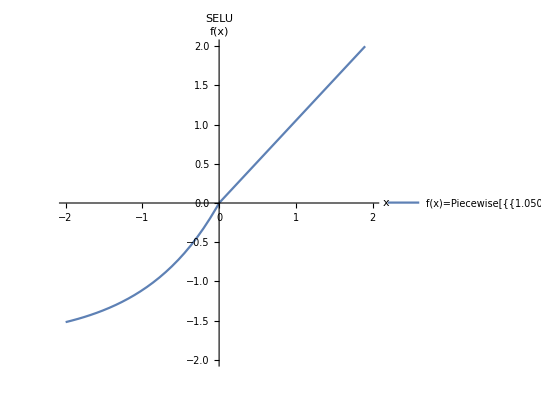

```mathematica
selu=Plot[Piecewise[{{1.7581(Exp[x]-1),x<0},{1.0507x,x>0}}], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=Piecewise[{{1.0507x, x≥0}, {1.7581(e^x-1), x<0}}]"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["SELU",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\SELU.jpg",selu]
```

C:\Modulation\Activation functions\SELU.jpg

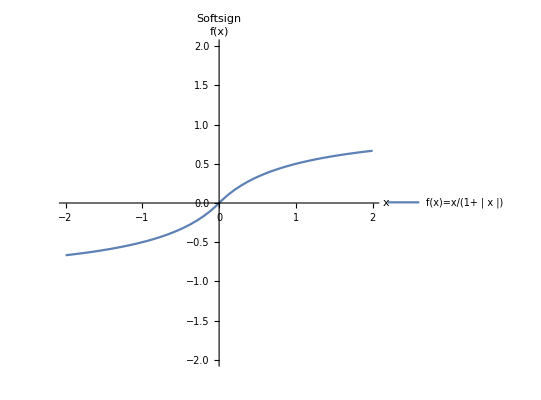

```mathematica
softsign=Plot[x/(1+Abs[x]), {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=x/(1+ | x |)"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["Softsign",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\Sosfsign.jpg",softsign]
```

C:\Modulation\Activation functions\Sosfsign.jpg

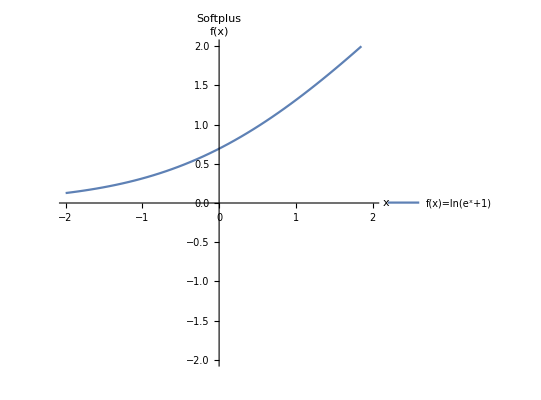

```mathematica
softplus=Plot[Log[Exp[x]+1], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=ln(e^x+1)"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["Softplus",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\Sosfplus.jpg",softplus]
```

C:\Modulation\Activation functions\Sosfplus.jpg

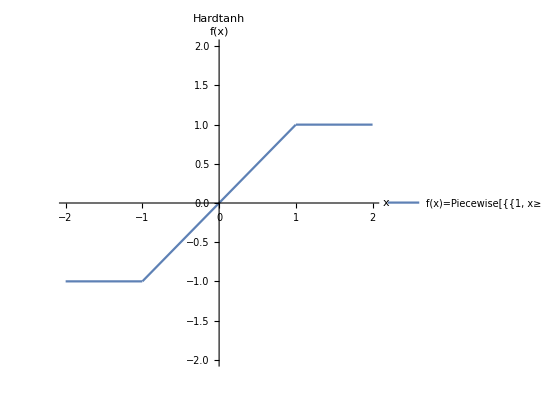

```mathematica
hardtanh=Plot[Clip[x,{-1,1}], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=Piecewise[{{1, x≥1}, {x, -1<x<1}, {-1, x≤-1}}]"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["Hardtanh",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\Hardtanh.jpg",hardtanh]
```

C:\Modulation\Activation functions\Hardtanh.jpg

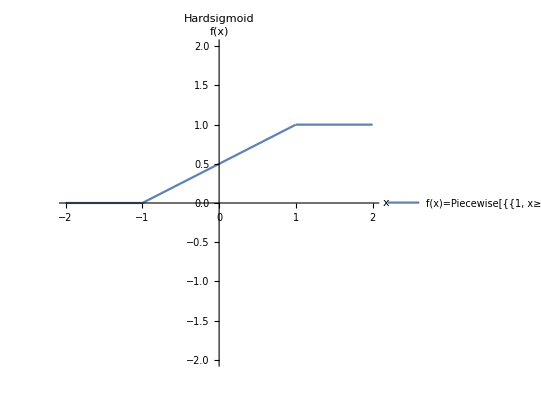

```mathematica
hardsigmoid=Plot[Clip[(x+1)/2, {0,1}], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=Piecewise[{{1, x≥1}, {(x+1)/2, -1<x<1}, {0, x≤-1}}]"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["Hardsigmoid",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\Hardsigmoid.jpg",hardsigmoid]
```

C:\Modulation\Activation functions\Hardsigmoid.jpg

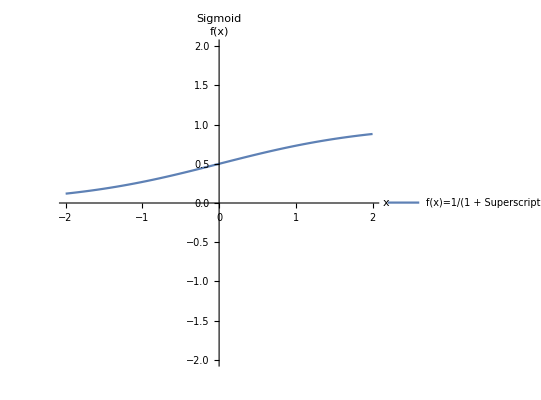

```mathematica
sigmoid=Plot[LogisticSigmoid[x], {x,-2,2},PlotRange->{{-2,2},{-2,2}},AspectRatio->1,PlotLegends->LineLegend[{"f(x)=1/(1 + SuperscriptBox[e, -x])"},LegendFunction->Framed],AxesLabel->{Style["x",FontSize->20,Plain,Gray],Style["f(x)",FontSize->20,Plain,Gray]},PlotLabel->Style["Sigmoid",40]]
```

```mathematica
Export["C:\\Modulation\\Activation functions\\Sigmoid.jpg",sigmoid]
```

C:\Modulation\Activation functions\Sigmoid.jpg